```mathematica
<<SymbolicComputing`
<<Notation`
Symbolize[ParsedBoxWrapper[SubscriptBox["_","_"]]]                                (* To use variables with subscripts! *)
DateString[]
$Version
$SCVersion
```

Wed 12 Apr 2023 17:06:50

13.2.0 for Microsoft Windows (64-bit) (November 18, 2022)

6.0.2 (June 28, 2021)

## Lecture 11 edited by Chi-Ok Hwang, originally made by Dr. 전 경원

[1] C. Arangala and K. A. Yokley, Exploring Calculus: Labs and Projects with Mathematica, 1st ed. Chapman and Hall/CRC, 2016.

-Graphics-

MathSymbolica Package

Winners of Wolfram Innovator Award 2017

-Graphics-

## Practice of SCSolve

```mathematica
Solve[x^2+a x+1==0,x]
```

{{x→1/2 (-a-√(-4+a^2))},{x→1/2 (-a+√(-4+a^2))}}

Solve simultaneous equations in x and y:

```mathematica
Solve[a x+y==7&&b x-y==1,{x,y}]
```

{{x→8/(a+b),y→-(a-7 b)/(a+b)}}

Solve an equation over the reals:

```mathematica
Solve[(x^2+2)(x^2-2)==0,x,Reals]
```

{{x→-√2},{x→√2}}

Solve an equation over the positive integers:

```mathematica
Solve[x^2+2y^3==3681&&x>0 &&y>0,{x,y},Integers]
```

{{x→15,y→12},{x→41,y→10},{x→57,y→6}}

Solve equations in a geometric region:

```mathematica
Solve[{x,y}∈InfiniteLine[{{0,0},{2,1}}]&&{x,y}∈Circle[],{x,y}]
```

{{x→-2/(√5),y→-1/(√5)},{x→2/(√5),y→1/(√5)}}

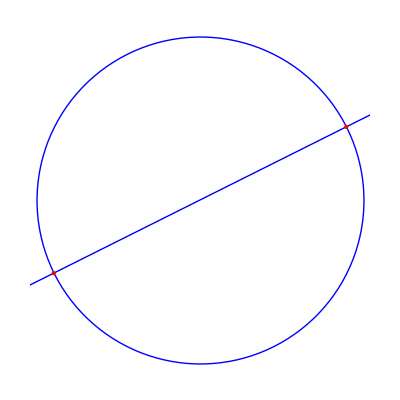

```mathematica
Graphics[{{Blue,InfiniteLine[{{0,0},{2,1}}],Circle[]},{PointSize[Large],Red,Point[{x,y}]/.%}}]
```

```mathematica
Solve[{x^2+y^2==1,x^2-y^2==-1},{x,y}]
```

{{x→0,y→-1},{x→0,y→1}}

```mathematica
Solve[{x^2+y^2==1,x^2-y^2==-1},{x^2,y^2}]
```

Solve::ivar: x^2 is not a valid variable.

Solve[{x^2+y^2==1,x^2-y^2==-1},{x^2,y^2}]

```mathematica
SCSolve[{x^2+y^2==1,x^2-y^2==-1},{x^2,y^2}]
```

{x^2==0,y^2==1}

```mathematica
SCSolve[{x^2+y^2==1,x^2-y^2==-1},{x^2,y^2},Thread->False]
```

{x^2,y^2}=={0,1}

```mathematica
SCSolve[{x^2+y^2==1,x^2-y^2==-1},{x,y}]
```

{{x==0,y==-1},{x==0,y==1}}

```mathematica
Ε==√(p^2 c^2+m^2 c^4)
SCSolve[%,p]
SCSolve[%%,p,-1]
```

Ε==√(c^4 m^2+c^2 p^2)

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{p==-(√(-c^4 m^2+Ε^2))/c},{p==(√(-c^4 m^2+Ε^2))/c}}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

p==(√(-c^4 m^2+Ε^2))/c

```mathematica
SCSolve[P[A,B]==P[A]P[B|A],P[B|A]]
```

P[B|A]==P[A,B]/P[A]

For root-finding functions other than Solve, use the Apply option in SCMAF as shown in the following example.

FindRoot[f,{x,Subscript[x, 0]}] 
searches for a numerical root of f, starting from the point x=Subscript[x, 0].

```mathematica
-5 (-1+ⅇ^x)+ⅇ^x x==0
SCMAF[%,FindRoot,{All,{x,5}},ChangeHead->SCRuleToEqual]
```

-5 (-1+ⅇ^x)+ⅇ^x x==0

x==4.96511

## Practice of SCEliminate

Eliminate the variable y between two equations:

```mathematica
Eliminate[{x==2+y,y==z},y]
```

2+z==x

### Applications (2)

Rewrite f in terms of a and b:

```mathematica
Eliminate[{f==x^5+y^5,a==x+y,b==x y},{x,y}]
```

f==a^5-5 a^3 b+5 a b^2

Find a condition for two polynomials to have a common root:

```mathematica
f=a x^3+(a^2-1)x^2+(2a-3)x+4;
g=(1-a^2)x^4-2a x+7a^2-1;
Eliminate[f==0&&g==0,x]
```

-102 a-2270 a^2+4602 a^3+2549 a^4-9336 a^5+1749 a^6+7464 a^7-4122 a^8-3102 a^9+2372 a^10+546 a^11-623 a^12+49 a^14==0

```mathematica
Resolve[Exists[x,f==0&&g==0]]
```

```mathematica
a==0||-102-2270 a+4602 a^2+2549 a^3-9336 a^4+1749 a^5+7464 a^6-4122 a^7-3102 a^8+2372 a^9+546 a^10-623 a^11+49 a^13==0
```

a==0||-102-2270 a+4602 a^2+2549 a^3-9336 a^4+1749 a^5+7464 a^6-4122 a^7-3102 a^8+2372 a^9+546 a^10-623 a^11+49 a^13==0

```mathematica
Resultant[f,g,x]
```

102 a+2270 a^2-4602 a^3-2549 a^4+9336 a^5-1749 a^6-7464 a^7+4122 a^8+3102 a^9-2372 a^10-546 a^11+623 a^12-49 a^14

```mathematica
SCEliminate[{x+y==1,2y==1},y]
```

1/2+x==1

```mathematica
SCEliminate[{x+y==1,y^2==1},y,2,Solve->x]
```

{{x==2},{x==0}}

```mathematica
SCEliminate[{(h c)/λ==(h c)/Subscript[λ, 1]+1/2 m v^2,h/λ==h/Subscript[λ, 1] Cos[θ]+m v Cos[Subscript[θ, e]],h/Subscript[λ, 1] Sin[θ]==m v Sin[Subscript[θ, e]]},v,3]
```

{(c h)/λ==(c h)/λ_1+(h^2 Csc[θ_e]^2 Sin[θ]^2)/(2 m λ_1^2),h/λ==(h Cos[θ])/λ_1+(h Cot[θ_e] Sin[θ])/λ_1}

In the following example, the third equation was used as the argument instead of the index number 3.

```mathematica
SCEliminate[{(h c)/λ==(h c)/Subscript[λ, 1]+1/2 m v^2,h/λ==h/Subscript[λ, 1] Cos[θ]+m v Cos[Subscript[θ, e]],h/Subscript[λ, 1] Sin[θ]==m v Sin[Subscript[θ, e]]},v,h/Subscript[λ, 1] Sin[θ]==m v Sin[Subscript[θ, e]]]
```

{(c h)/λ==(c h)/λ_1+(h^2 Csc[θ_e]^2 Sin[θ]^2)/(2 m λ_1^2),h/λ==(h Cos[θ])/λ_1+(h Cot[θ_e] Sin[θ])/λ_1}

In the following example, the variable z is eliminated from the equation set by solving the last equation for z.

```mathematica
SCEliminate[{x+y+z==1,x-y==0},y+2z==2,z,Solve->{x,y},Keep->True]
```

{x==0,y==0,y+2 z==2}

```mathematica
Resultant[x^2-2x+7,x^3-x+5,x]
```

265

```mathematica
Resultant[x^2+2x-3,x^2+x-2,x]
```

0

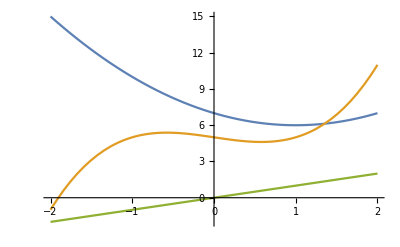

```mathematica
Plot[{x^2-2x+7,x^3-x+5,x},{x,-2,2}]
```

SlotSequence (##)
Function (&)
Apply (@@)

```mathematica
ClearAll["Global`*"]
Solve[x^2-2x+7==0,x]
```

{{x→1-ⅈ √6},{x→1+ⅈ √6}}

```mathematica
ClearAll["Global`*"]
Solve[x^2-2x+7==0,x];
Flatten[%]
```

{x→1-ⅈ √6,x→1+ⅈ √6}

```mathematica
ClearAll["Global`*"]
Solve[x^2-2x+7==0,x];
a=Values[Flatten[%]]
```

{1-ⅈ √6,1+ⅈ √6}

```mathematica
NSolve[x^3-x+5==0,x]
b=Values[Flatten[%]]
1##&@@Flatten[Table[a[[i]]-b[[j]],{i,1,2},{j,1,3}]] 
N[%]//Chop
```

{1-ⅈ √6,1+ⅈ √6}

{{x→-1.90416},{x→0.95208-1.31125 ⅈ},{x→0.95208+1.31125 ⅈ}}

{-1.90416,0.95208-1.31125 ⅈ,0.95208+1.31125 ⅈ}

265.+2.84217×10^-14 ⅈ

265.

```mathematica
ClearAll["Global`*"]
a=SCMAF[x^2-2x+7==0,Solve,{All,x},Flatten,{All},Values,{All}]
b=SCMAF[x^2-x+5==0,Solve,{All,x},Flatten,{All},Values,{All}]
Flatten[Table[a[[i]]-b[[j]],{i,1,2},{j,1,2}]] 
1 ##&@@ % 
N[%]
```

{x→1-ⅈ √6,x→1+ⅈ √6}

{1-ⅈ √6,1+ⅈ √6}

{x→1/2 (1-ⅈ √19),x→1/2 (1+ⅈ √19)}

{1/2 (1-ⅈ √19),1/2 (1+ⅈ √19)}

{1-ⅈ √6+1/2 (-1+ⅈ √19),1-ⅈ √6+1/2 (-1-ⅈ √19),1+ⅈ √6+1/2 (-1+ⅈ √19),1+ⅈ √6+1/2 (-1-ⅈ √19)}

(1-ⅈ √6+1/2 (-1-ⅈ √19))(1+ⅈ √6+1/2 (-1-ⅈ √19))(1-ⅈ √6+1/2 (-1+ⅈ √19))(1+ⅈ √6+1/2 (-1+ⅈ √19))

7.+0. ⅈ

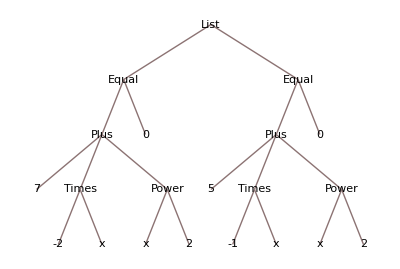

```mathematica
{x^2-2x+7==0,x^2-x+5==0}//TreeForm
```

Apply (@@)
f@@expr orApplypaclet:ref/Apply[f,expr] 
replaces the head of expr by f.

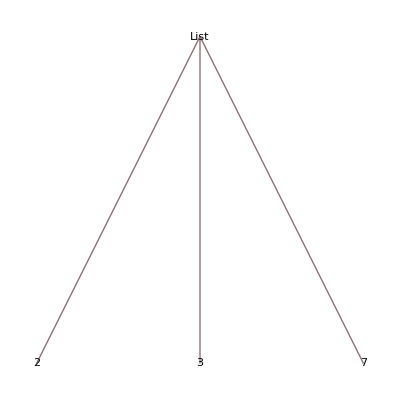

42

42

42

«1 more identical outputs»

```mathematica
{2,3,7} //TreeForm
Apply[Times,{2,3,7}]
Times[2,3,7]
Times@@ {2,3,7}
Times@@# [2,3,7]
```

```mathematica
ClearAll["Global`*"]
{x^2-2x+7==0,x^3-x+5==0}
SCMAF[%,NSolve,{All,x},Level->1,Post->{Values,Flatten},$,
Outer[Subtract,Sequence@@#]&,All,
Post->Flatten,
Times@@ #&,All,Post->{Chop}]
```

{7-2 x+x^2==0,5-x+x^3==0}

{{1.-2.44949 ⅈ,1.+2.44949 ⅈ},{-1.90416,0.95208-1.31125 ⅈ,0.95208+1.31125 ⅈ}}

```mathematica
ClearAll["Global`*"]
{{1.-2.449489742783178 ⅈ,1.+2.449489742783178 ⅈ},{-1.9041608591349206,0.9520804295674603-1.3112480440771224 ⅈ,0.9520804295674603+1.3112480440771224 ⅈ}}
SCMAF[%,Outer[Subtract,Sequence@@#]& ,{All},Post-> Flatten,Times @@ # &,All, Post->Chop]
```

{{1.-2.44949 ⅈ,1.+2.44949 ⅈ},{-1.90416,0.95208-1.31125 ⅈ,0.95208+1.31125 ⅈ}}

{2.90416-2.44949 ⅈ,0.0479196-1.13824 ⅈ,0.0479196-3.76074 ⅈ,2.90416+2.44949 ⅈ,0.0479196+3.76074 ⅈ,0.0479196+1.13824 ⅈ}

265.

```mathematica
ClearAll["Global`*"]
{x^2-2x+7==0,x^3-x+5==0}
SCMAF[%,NSolve,{All,x},Level->1,Post->{Values,Flatten},
Outer[Subtract,Sequence@@#]&,All,
Post->Flatten, Times @@ # &,All,
Post->{Chop,Expand}]
```

{7-2 x+x^2==0,5-x+x^3==0}

{2.90416-2.44949 ⅈ,0.0479196-1.13824 ⅈ,0.0479196-3.76074 ⅈ,2.90416+2.44949 ⅈ,0.0479196+3.76074 ⅈ,0.0479196+1.13824 ⅈ}

265.

```mathematica
x^3-x+c==0
Solve[%,x]/.c->5
N[%]
```

c-x+x^3==0

{{x→-(-1)^(2/3) (2/(3 (45-√2013)))^(1/3)+(1/2 (-45+√2013))^(1/3)/3^(2/3)},{x→(-1/2)^(2/3) (1+ⅈ √3) 1/(3 (45-√2013))^(1/3)-((1-ⅈ √3) (1/2 (-45+√2013))^(1/3))/(2 3^(2/3))},{x→(-1/2)^(2/3) (1-ⅈ √3) 1/(3 (45-√2013))^(1/3)-((1+ⅈ √3) (1/2 (-45+√2013))^(1/3))/(2 3^(2/3))}}

{{x→0.95208-1.31125 ⅈ},{x→-1.90416+4.70776×10^-16 ⅈ},{x→0.95208+1.31125 ⅈ}}

```mathematica
ClearAll["Global`*"]
x^3-x+5==0
SCMAF[%,NSolve,{All,x},$,Flatten,{All},Values,{All}]
```

5-x+x^3==0

{{x→-1.90416},{x→0.95208-1.31125 ⅈ},{x→0.95208+1.31125 ⅈ}}

```mathematica
ClearAll["Global`*"]
x^3-x+5==0
SCMAF[%,NSolve,{All,x},Flatten,{All},Values,{All}]
```

5-x+x^3==0

{x→-1.90416,x→0.95208-1.31125 ⅈ,x→0.95208+1.31125 ⅈ}

{-1.90416,0.95208-1.31125 ⅈ,0.95208+1.31125 ⅈ}

Find intersection points of f(x)=sin(x) and g(x)=cos(x) for x between 0 and 2π.

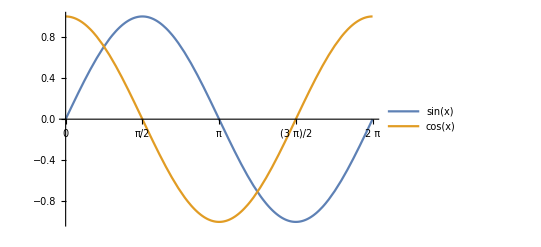

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2π},Ticks->{{0,π/2,π,3/2 π,2π},Automatic},PlotLegends->"Expressions"]
```

```mathematica
{f[x]==Sin[x],g[x]==Cos[x]}
SCMAF[%,SCEliminate,{All,f[x]==g[x],{f[x],g[x]}},
And,{All,0≤x≤2π},
SCSolve,{All,x},
FullSimplify,{All},Level->{3}]
```

{f[x]==Sin[x],g[x]==Cos[x]}

{{x==-2 ArcTan[1-√2]},{x==2 π-2 ArcTan[1+√2]}}

{{x==π/4},{x==(5 π)/4}}

## Practice

```mathematica
∑_(m=0)^∞ Subscript[a, m] Subscript[f, m][r] ⅇ^(ⅈ m(θ-Subscript[θ, 0]))
SCMAF[%,SCApplyFunc,{All,(ⅆ#)/ⅆr&},Hold->Subscript[θ, 0],Apply->SCEvalDeriv]
∑_(m=0)^∞ ⅇ^(ⅈ m (θ-Subscript[θ, 0])) Subscript[a, m] Subscript[f, m][r]
∑_(m=0)^∞ ⅇ^(ⅈ m (θ-Subscript[θ, 0])) Subscript[a, m] Subscript[f, m]'[r]
```

∑_(m=0)^∞ a_m ⅇ^(ⅈ m (θ-θ_0)) f_m[r]

SCEvalDeriv

∑_(m=0)^∞ a_m ⅇ^(ⅈ m (θ-θ_0)) f_m[r]

∑_(m=0)^∞ a_m ⅇ^(ⅈ m (θ-θ_0)) f_m'[r]

## Rates of Change

### Introduction

Average velocity is the rate of change of output values over an interval of input values. Instantaneous velocity or velocity is the rate of change of output values at a single input value.

Exercises:

Let the cumulative sales of a new type of tablet  be modeled by
s(x)=0.17(4.2^x) milion units
where x=0 is the beginning of the fiscal year. Note that the units of x are in years.

a. Find the slope of the line that passes through the function, s(x) for tablet sales through x=0 and x=2.

s==0.17 4.2^x

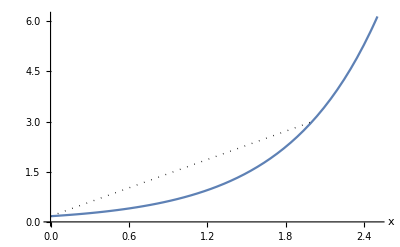

```mathematica
s==0.17 4.2^x
SCMAF[%,Plot,{At[2],{x,0,2.5},Epilog->{Dotted,Line[{{x,0.17 4.2^x}/.x->0,{x,0.17 4.2^x}/.x->2}]},AxesLabel->Automatic},Part->2]
```

```mathematica
m==(s[Subscript[x, 2]]-s[Subscript[x, 1]])/(Subscript[x, 2]-Subscript[x, 1])
SCMAF[%,RA,{At[2],s[x_]==0.17(4.2^x)},
RA,{At[2],{Subscript[x, 1]==0,Subscript[x, 2]==2}}]
```

m==(-s[x_1]+s[x_2])/(-x_1+x_2)

m==(-0.17 4.2^x_1+0.17 4.2^x_2)/(-x_1+x_2)

m==1.4144

b. Determine the units of the slope.

```mathematica
m==(s[Subscript[x, 2]]-s[Subscript[x, 1]])/(Subscript[x, 2]-Subscript[x, 1])
SCMAF[%,RA,{At[2],s[x_]==0.17(4.2^(x/"Years"))"Million Units"},
RA,{At[2],{Subscript[x, 1]==0"Years",Subscript[x, 2]==2"Years"}}]
```

m==(-s[x_1]+s[x_2])/(-x_1+x_2)

m==1/(-x_1+x_2)(-0.17 4.2^(x_1/Years) Million Units+0.17 4.2^(x_2/Years) Million Units)

m==(1.4144 Million Units)/Years

c. Determine what the slope we found, represents in terms of rates of change.

m of part a. is an average velocity.

d. Find an equation for the line that passes through s(x) at x=0 and x=2.

without units

```mathematica
y-Subscript[y, 0]==m(x-Subscript[x, 0])
SCMAF[%,RA,{All,{m==1.4144}},
RR,{All,{Subscript[y, 0]==s[Subscript[x, 1]],Subscript[x, 0]==Subscript[x, 1],s[x_]==0.17(4.2^x),Subscript[x, 1]==0}},
SCSolve,{All,y}]
```

y-y_0==m (x-x_0)

-0.17+y==1.4144 x

y==0.17+1.4144 x

with units.

```mathematica
y-Subscript[y, 0]==m(x-Subscript[x, 0])
SCMAF[%,RA,{All,{m==(1.4144 "Million Units")/("Years")}},
RR,{All,{Subscript[y, 0]==s[Subscript[x, 1]],Subscript[x, 0]==Subscript[x, 1],s[x_]==0.17(4.2^(x/"Years"))"Million Units",Subscript[x, 1]==0}},
SCSolve,{All,y}]
```

y-y_0==m (x-x_0)

-0.17 Million Units+y==(1.4144 Million Units x)/Years

y==0.17 Million Units+(1.4144 Million Units x)/Years

e. Plot s(x) and the line.

{s[x_]==0.17 4.2^x,y==0.17+1.4144 x}

{0.17 4.2^x,0.17+1.4144 x}

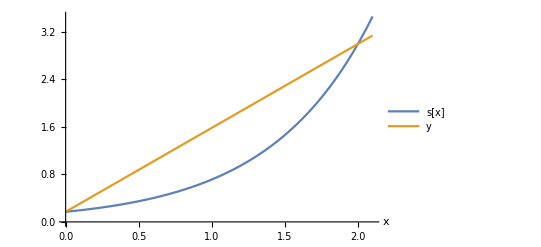

```mathematica
{s[x_]==0.17(4.2^x),y==0.17+1.4144 x}
SCMAF[%,Part,{All,2},Level->{1},
Plot,{All,{x,0,2.1},AxesLabel->Automatic,PlotLegends->{"s[x]","y"}}]
```

f, g. Determine how quickly sales of the tablets are changing exactly at the end of the second year.

```mathematica
Manipulate[Module[{s,sol,y,x},
s[x_]:=0.17(4.2^x);
sol=Solve[y-s[2]==(s[2]-s[x0])/(2-x0)(x-2),y][[1]];
Plot[{s[x],Labeled[y/.sol,(s[2]-s[x0])/(2-x0)]},{x,0,2.1},PlotRange->{0,3.5},PlotLegends->{"s[x]","y"}]
],{x0,0,1.999}]
```

Optimize the manipulate by replacing the Solve expression with a explicit form of line equation.

```mathematica
y-y1==m(x-x1)
SCMAF[%,RA,{At[2],m==(y2-y1)/(x2-x1)},
SCSolve,{All,y}]
```

y-y1==m (x-x1)

y-y1==((x-x1) (-y1+y2))/(-x1+x2)

y==(x y1-x2 y1-x y2+x1 y2)/(x1-x2)

```mathematica
Manipulate[Module[{s,sol,y,x,x1,x2,y1,y2},
s[x_]:=0.17(4.2^x);
y[x_]:=(x y1-x2 y1-x y2+x1 y2)/(x1-x2)/.{x1->2,y1->s[2],x2->x0,y2->s[x0]};
Plot[{s[x],Labeled[y[x],(s[x0]-s[2])/(x0-2)]},{x,1.9,3.1},PlotRange->{2,14},PlotLegends->{"s[x]","y"}]
],{{x0,3},2.001,3}]
```

## Going on Another Tangent

### Introduction

A secant line to a curve is a line that intersects the curve at 2 points. A tangent line to a curve at a given point is a line that just touches the curve at that point.

The slope of the tangent line can be found by

```mathematica
SCLimit[(f[x]-f[Subscript[x, 0]])/(x-Subscript[x, 0]),x->Subscript[x, 0]]
```

lim_(x→x_0) (f[x]-f[x_0])/(x-x_0)

```mathematica
SCARA[lim_(x->Subscript[x, 0]) (f[x]-f[Subscript[x, 0]])/(x-Subscript[x, 0]),{(x->Subscript[x, 0])->(h->0),x->Subscript[x, 0]+h},Hold->Subscript[x, 0]]
```

lim_(x→x_0) (f[x]-f[x_0])/(x-x_0)==lim_(h→0) (-f[x_0]+f[h+x_0])/h

### The Derivative of a Function at a Point

Demonstration: The Tangent Line Problem

```mathematica
Manipulate[Module[{y,yp,m,x0=5},
y[x_]:=√x;
m=Limit[(y[x]-y[x0])/(x-x0),x->x0+h];
yp[x_]:=m(x-x0)+y[x0];
Plot[{y[x],yp[x]},{x,0,20},PlotRange->{0,5},
Epilog->{Inset["incline: "<>ToString@N@m],Style[Point@{5,y[5]},PointSize[Medium],Red]}]
],{h,10,0,1}]
```

### Linearization

A tangent line to a function f(x) at x_0 is a very good approximation to f(x) for x values very close to x_0. This idea is called linearization.

Exercises

a. Plot f(x)=x^2-5.

f[x]==-5+x^2

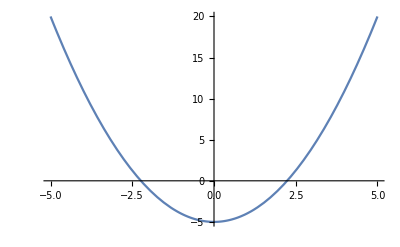

```mathematica
f[x]==x^2-5
SCMAF[%,Plot,{At[2],{x,-5,5}},Take->{2}]
```

b. Find the equation of the tangent line to f(x) at x=2.

```mathematica
m==lim_(x->Subscript[x, 0]) (f[x]-f[Subscript[x, 0]])/(x-Subscript[x, 0])
SCMAF[%,RA,{At[2],f[x_]->x^2-5},Post->SCEvalLimit,
RA,{All,Subscript[x, 0]->2}]
```

m==lim_(x→x_0) (f[x]-f[x_0])/(x-x_0)

m==2 x_0

m==4

```mathematica
y-Subscript[y, 0]==m(x-Subscript[x, 0])
SCMAF[%,RR,{All,{Subscript[x, 0]->2,Subscript[y, 0]->f[2],m->4}},
RA,{All,{f[x_]==x^2-5,f'[x_]==2 x}},
SCSolve,{All,y}]
```

y-y_0==m (x-x_0)

1+y==4 (-2+x)

y==-9+4 x

{f[x]==-5+x^2,y==-9+4 x}

{f[x],y}=={-5+x^2,-9+4 x}

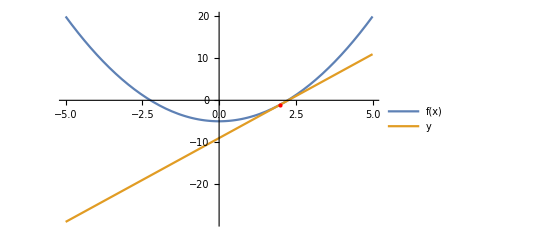

```mathematica
{f[x]==x^2-5,y==-9+4 x}
SCMAF[%,Thread,{All,Equal},
Plot,{At[2],{x,-5,5},Epilog->{Red,PointSize[Medium],Point[{{x,x^2-5}/.x->2}]},PlotLegends->At[1]},Take->{2}]
```

c. Find the value of √5 using the tangent line.

```mathematica
y==-9+4 x
SCMAF[%,RA,{All,y==0},
SCSolve,{All,x},Apply->N]
```

y==-9+4 x

0==-9+4 x

x==2.25

Prove lim_(θ→0) (sin θ)/θ=1.

-Graphics-
https://commons.wikimedia.org/wiki/File:Sinx_x _limit _proof.svg

```mathematica
Subscript[S, KOA]≤Subscript[S, KOA]'≤Subscript[S, LOA]
SCMAF[%,RA,{All,{Subscript[S, KOA]==(Cos[θ]Abs[Sin[θ]])/2,Subscript[S, KOA]'==π Abs[θ]/(2π),Subscript[S, LOA]==Abs[Tan[θ]]/2}},
SCMultEq,{All,2/Abs[Sin[θ]]},Post->SCRecipIneq,
Simplify,{All,Assumptions->{-π/2<θ<π/2}}]
```

S_KOA≤S_KOA'≤S_LOA

(Sec[θ]≤0&&(((|Sin[θ]|)/(|θ|)≤Sec[θ]&&((|Sin[θ]|)/(|Tan[θ]|)≤(|Sin[θ]|)/(|θ|)||(|Sin[θ]|)/(|Tan[θ]|)≥0))||((|Sin[θ]|)/(|θ|)≥0&&0<(|Sin[θ]|)/(|Tan[θ]|)≤(|Sin[θ]|)/(|θ|))))||(Sec[θ]≥0&&0<(|Sin[θ]|)/(|θ|)≤Sec[θ]&&0<(|Sin[θ]|)/(|Tan[θ]|)≤(|Sin[θ]|)/(|θ|))

0<(|Sin[θ]|)/(|Tan[θ]|)≤(|Sin[θ]|)/(|θ|)&&0<(|Sin[θ]|)/(|θ|)≤Sec[θ]

```mathematica
(|Sin[θ]|)/(|Tan[θ]|)≤(|Sin[θ]|)/(|θ|)≤Sec[θ]
SCMAF[%,SCLimit,{All,θ -> 0},Level->{1},
SCEvalLimit,{{At[1]},{At[3]}}]
```

(|Sin[θ]|)/(|Tan[θ]|)≤(|Sin[θ]|)/(|θ|)≤Sec[θ]

lim_(θ→0) (|Sin[θ]|)/(|Tan[θ]|)≤lim_(θ→0) (|Sin[θ]|)/(|θ|)≤lim_(θ→0) Sec[θ]

1≤lim_(θ→0) (|Sin[θ]|)/(|θ|)≤1

Therefore, lim_(θ→0) (sin θ)/θ=1 by the squeeze theorem.

Prove lim_(θ→0) (1-cos θ)/θ.

```mathematica
SCAFE[SCLimit[(1-Cos[θ])/θ,θ -> 0],SCMultFrac,{All,1+Cos[θ],Post->Expand}]
```

lim_(θ→0) (1-Cos[θ])/θ==lim_(θ→0) (1-Cos[θ]^2)/(θ+θ Cos[θ])

```mathematica
SCMAF[%,TrigFactor,{1-Cos[θ]^2},
SCFactor,{θ+θ Cos[θ],θ},
RA,{At[2],SCLimit[Sin[θ]^2/(θ (1+Cos[θ])),θ -> 0]==SCLimit[Sin[θ]/θ,θ -> 0]SCLimit[Sin[θ]/(1+Cos[θ]),θ -> 0]},
SCEvalLimit,At[2]]
```

lim_(θ→0) (1-Cos[θ])/θ==(lim_(θ→0) Sin[θ]/θ)lim_(θ→0) Sin[θ]/(1+Cos[θ])

lim_(θ→0) (1-Cos[θ])/θ==0

## Practice of SCEvalLimit

```mathematica
SCEvalLimit[SCLimit[Sin[θ]/(1+Cos[θ]),θ->0]]
```

0

```mathematica
SCLimit[Sin[θ]/(1+Cos[θ]),θ->0]
SCEvalLimit[%]
```

lim_(θ→0) Sin[θ]/(1+Cos[θ])

0

## Practice of SCMultFrac

```mathematica
SCMultFrac[(a+b/c)/(a+x+d/c),c]
```

(b+a c)/(a c+d+c x)

```mathematica
SCMultFrac[(a+b/c)/(a+x/c+d/(a+b/c)),c]
```

(b+a c)/(a c+(c d)/(a+b/c)+x)

```mathematica
SCMultFrac[(a+b/c)/(a+x/c+d/(a+b/c)),c,Repeat->True]
```

(b+a c)/(a c+(c^2 d)/(b+a c)+x)

```mathematica
SCMultFrac[(√(a+b/c^2))/(a+x+d/c)^2,c]
```

(c √(b+a c^2))/(√(c^2) (a √c+d/(√c)+√c x)^2)

```mathematica
SCMultFrac[(√(a+b/c^2))/(a+x+d/c)^2,c,c^2]
```

(√(c^2) √(b+a c^2))/(a c+d+c x)^2

```mathematica
SCMultFrac[(√(a+b/c^2))/(a+x+d/c)^2,c,c^2,Positive->True]
```

(c √(b+a c^2))/(a c+d+c x)^2

```mathematica
SCMultFrac[((a+b/c^2)^n)/(a+x+d/c)^2,c^(2n)]
```

(c^(2 n) ((c^(2 n))^(1/n))^-n (b+a c^2)^n)/((a √(c^(2 n))+(√(c^(2 n)) d)/c+√(c^(2 n)) x)^2)

```mathematica
SCMultFrac[((a+b/c^2)^n)/(a+x+d/c)^2,c^(2n),c^2]
```

(c^2 ((c^(2 n))^(1/n))^-n (b+a c^2)^n)/(a c+d+c x)^2

```mathematica
SCMultFrac[((a+b/c^2)^n)/(a+x+d/c)^2,c^(2n),c^2,Positive->True]
```

(c^(2-2 n) (b+a c^2)^n)/(a c+d+c x)^2

```mathematica
SCMultFrac[(a+b)/(c+d),f]
```

(a+b)/(c+d)

```mathematica
SCMultFrac[(a+b)/(c+d),f,Force->True]
```

(a f+b f)/(c f+d f)

## Basic Derivative Rules

### Introduction

Derivative notations of Wolfram Language.

```mathematica
{f'[x],f''[x],Derivative[3][f][x]};
```

SymbolicComputing package also provides a fractional form of derivatives.

```mathematica
ⅆf[x]/ⅆx;
```

### Basic Properties of Derivatives

```mathematica
ⅆ/ⅆx x^0
```

0

```mathematica
SCAFE[ⅆc/ⅆx,SCEvalDeriv]
```

ⅆc/ⅆx==0

```mathematica
SCAFE[(ⅆ x^n)/ⅆx,SCEvalDeriv]
```

(ⅆ x^n)/ⅆx==n x^(-1+n)

```mathematica
SCAFE[(ⅆ(c x^n))/ⅆx,SCEvalDeriv]
```

(ⅆ(c x^n))/ⅆx==c n x^(-1+n)

```mathematica
SCAFE[ⅆ/ⅆx(f[x]+g[x]),SCEvalDeriv,Post->SCAbbrevDeriv]
```

(ⅆ(f[x]+g[x]))/ⅆx==ⅆf/ⅆx+ⅆg/ⅆx

```mathematica
SCAFE[ⅆ/ⅆx(f[x]+g[x]),SCDerivExpand]
```

(ⅆ(f[x]+g[x]))/ⅆx==ⅆf[x]/ⅆx+ⅆg[x]/ⅆx

```mathematica
SCAFE[(ⅆ(c f[x]))/ⅆx,SCDerivExpand]
```

(ⅆ(c f[x]))/ⅆx==c ⅆf[x]/ⅆx

### Part Multilevel Specifications

```mathematica
{{a,b,c},{d,e,f},{g,h,i}}[[2,3]]
```

f

```mathematica
{{a,b,c},{d,e,f},{g,h,i}}[[All,2]]
```

{b,e,h}

```mathematica
(* Pick out parts 2 and 3 of part 1 and
 Pick out parts 2 and 3 of part 3: *)
```

```mathematica
{{a,b,c},{d,e,f},{g,h,i}}[[{1,3},{2,3}]]
```

{{b,c},{h,i}}

### Level command

```mathematica
SCLimit[(Sin[x+h]-Sin[x])/h,h->0]
```

lim_(h→0) (-Sin[x]+Sin[h+x])/h

```mathematica
Level[ⅆSin[x]/ⅆx==lim_(h->0) (-Sin[x]+Sin[h+x])/h,2]
Level[ⅆSin[x]/ⅆx==lim_(h->0) (-Sin[x]+Sin[h+x])/h,2][[4]]
Level[ⅆSin[x]/ⅆx==lim_(h->0) (-Sin[x]+Sin[h+x])/h,2][[4,2]]
Level[ⅆSin[x]/ⅆx==lim_(h->0) (-Sin[x]+Sin[h+x])/h,2][[4,2,2]]
```

{Sin[x],x,ⅆSin[x]/ⅆx,(-Sin[x]+Sin[h+x])/h,h→0,lim_(h→0) (-Sin[x]+Sin[h+x])/h}

(-Sin[x]+Sin[h+x])/h

-Sin[x]+Sin[h+x]

Sin[h+x]

```mathematica
Level[ⅆSin[x]/ⅆx==lim_(h->0) (-Sin[x]+Sin[h+x])/h,0]
Level[ⅆSin[x]/ⅆx==lim_(h->0) (-Sin[x]+Sin[h+x])/h,1]
Level[ⅆSin[x]/ⅆx==lim_(h->0) (-Sin[x]+Sin[h+x])/h,{0,1}]
Level[ⅆSin[x]/ⅆx==lim_(h->0) (-Sin[x]+Sin[h+x])/h,{0,2}]
Level[ⅆSin[x]/ⅆx==lim_(h->0) (-Sin[x]+Sin[h+x])/h,{2}]
```

{}

{ⅆSin[x]/ⅆx,lim_(h→0) (-Sin[x]+Sin[h+x])/h}

{ⅆSin[x]/ⅆx,lim_(h→0) (-Sin[x]+Sin[h+x])/h,ⅆSin[x]/ⅆx==lim_(h→0) (-Sin[x]+Sin[h+x])/h}

{Sin[x],x,ⅆSin[x]/ⅆx,(-Sin[x]+Sin[h+x])/h,h→0,lim_(h→0) (-Sin[x]+Sin[h+x])/h,ⅆSin[x]/ⅆx==lim_(h→0) (-Sin[x]+Sin[h+x])/h}

{Sin[x],x,(-Sin[x]+Sin[h+x])/h,h→0}

### Derivatives of Trigonometric Functions

ⅆSin[x]/ⅆx==lim_(h→0) (-Sin[x]+Sin[h+x])/h

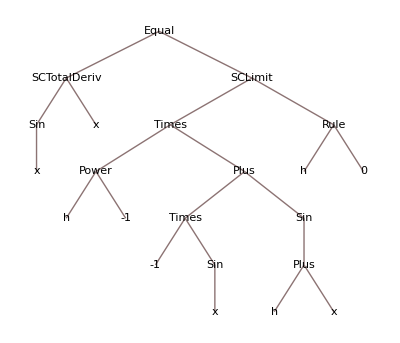

ⅆSin[x]/ⅆx==lim_(h→0) ((Cos[x] Sin[h])/h-Sin[x]/h+(Cos[h] Sin[x])/h)

ⅆSin[x]/ⅆx==lim_(h→0) (Cos[x] Sin[h])/h+lim_(h→0) (-Sin[x]/h+(Cos[h] Sin[x])/h)

ⅆSin[x]/ⅆx==Cos[x] lim_(h→0) Sin[h]/h+Sin[x] lim_(h→0) (-1/h+Cos[h]/h)

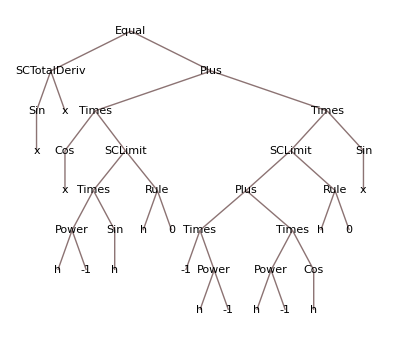

```mathematica
ⅆSin[x]/ⅆx==SCLimit[(Sin[x+h]-Sin[x])/h,h->0]
%//TreeForm
SCMAF[%,TrigExpand,At[2,1]]
SCMAF[%,SCExpandFunc,{At[2],SCLimit},Hold->-Sin[x]/h+(Cos[h] Sin[x])/h]
SCMAF[%,SCFactorFunc,{{At[2,1],SCLimit,-Cos[x]},{At[2,2],SCLimit,Sin[x]}}]
% //TreeForm
```

```mathematica
ⅆSin[x]/ⅆx==lim_(h->0) (-Sin[x]+Sin[h+x])/h
SCMAF[%,TrigExpand,At[2,1],
SCExpandFunc,{At[2],SCLimit},Hold->-Sin[x]/h+(Cos[h] Sin[x])/h,
SCFactorFunc,{{At[2,1],SCLimit,-Cos[x]},{At[2,2],SCLimit,Sin[x]}},Post->Simplify,
SCEvalLimit,At[2]]
```

ⅆSin[x]/ⅆx==lim_(h→0) (-Sin[x]+Sin[h+x])/h

ⅆSin[x]/ⅆx==Cos[x] lim_(h→0) Sin[h]/h+Sin[x] lim_(h→0) (-1+Cos[h])/h

ⅆSin[x]/ⅆx==Cos[x]

```mathematica
ⅆCos[x]/ⅆx==SCLimit[(Cos[x+h]-Cos[x])/h,h->0]
SCMAF[%,TrigExpand,At[1],Base->SCLimit[x_],
SCExpandFunc,{At[2],SCLimit},Hold->-Cos[x]/h+(Cos[h] Cos[x])/h,
SCFactorFunc,{{At[2,1],SCLimit,-Cos[x]},{At[2,2],SCLimit,-Sin[x]}},Post->Simplify,
Simplify,At[2],Post->SCEvalLimit]
```

ⅆCos[x]/ⅆx==lim_(h→0) (-Cos[x]+Cos[h+x])/h

ⅆCos[x]/ⅆx==lim_(h→0) (-Cos[x]+Cos[h+x])/h

ⅆCos[x]/ⅆx==-Sin[x]

## Derivative Rules (Continued)

### Product Rule

```mathematica
ClearAll["Global`*"]
SCAFE[(ⅆ(f[x]g[x]))/ⅆx,SCDerivExpand,Post->SCAbbrevFunc]
```

(ⅆ(f[x] g[x]))/ⅆx==g ⅆf/ⅆx+f ⅆg/ⅆx

```mathematica
(ⅆ f[x]g[x])/ⅆx==SCLimit[(f[x+h]g[x+h]-f[x]g[x])/h,h-> 0]
SCMAF[%,Apart,At[2,1],
RA,{At[2],{f[h+x] g[h+x]->f[h+x] g[h+x]-f[h+x] g[x],f[x] g[x]->f[x] g[x]-f[h+x] g[x]}},
Simplify,All,Level->{3},
SCExpandFunc,{At[2],SCLimit},Hold->{((-f[x]+f[h+x]) g[x])/h,(f[h+x] (-g[x]+g[h+x]))/h},
SCFactorFunc,{SCLimit[((-f[x]+f[h+x]) g[x])/h,h->0],SCLimit,g[x]},
RA,{At[2],SCLimit[(f[h+x] (-g[x]+g[h+x]))/h,h->0]==f[x]SCLimit[(-g[x]+g[h+x])/h,h->0]},
RA,{At[2],{SCLimit[(-f[x]+f[h+x])/h,h->0]==ⅆf[x]/ⅆx,SCLimit[(-g[x]+g[h+x])/h,h->0]==ⅆg[x]/ⅆx}}]
```

(ⅆf[x] g[x])/ⅆx==lim_(h→0) (-f[x] g[x]+f[h+x] g[h+x])/h

(ⅆf[x] g[x])/ⅆx==g[x] lim_(h→0) (-f[x]+f[h+x])/h+f[x] lim_(h→0) (-g[x]+g[h+x])/h

(ⅆf[x] g[x])/ⅆx==g[x] ⅆf[x]/ⅆx+f[x] ⅆg[x]/ⅆx

### Quotient Rule

```mathematica
SCAFE[ⅆ/ⅆx f[x]/g[x],SCDerivExpand,All,Post->SCAbbrevFunc]
```

ⅆ/ⅆx f[x]/g[x]==1/g ⅆf/ⅆx-f/g^2 ⅆg/ⅆx

```mathematica
SCAFE[ⅆ/ⅆx f[x]/g[x],SCDerivExpand,All]
```

ⅆ/ⅆx f[x]/g[x]==1/g[x] ⅆf[x]/ⅆx-f[x]/g[x]^2 ⅆg[x]/ⅆx

### Chain Rule

```mathematica
SCAFE[(ⅆ f[g[x]])/ⅆx,SCDerivExpand,All,Post ->SCAbbrevFunc]
```

ⅆf[g[x]]/ⅆx==f' ⅆg/ⅆx

```mathematica
SCAFE[(ⅆ f[g[x]])/ⅆx,SCDerivExpand,All]
SCAbbrevFunc[%]
```

ⅆf[g[x]]/ⅆx==f'[g[x]] ⅆg[x]/ⅆx

ⅆf/ⅆx==f' ⅆg/ⅆx

```mathematica
ⅆf[g[x]]/ⅆx==f' ⅆg/ⅆx
```

ⅆf[g[x]]/ⅆx==f' ⅆg/ⅆx